```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/tbent/projects/codim1/notes

```mathematica
Needs["OrthogonalPolynomials`"]
```

```mathematica
n=20;
w[t_,a_]:=1/(1 - a*t);
mom=Integrate[t^k *w[t,-0.5],{t,0.0,1.0}, Assumptions->{k≥0,Im[a]==0,a<1, a>-(10^307)}];
```

```mathematica
moments=Table[mom,{k,0,2 * n - 1}]
```

{0.81093,0.37814,0.243721,0.179225,0.14155,0.1169,0.0995338,0.0866466,0.0767068,0.0688087,0.0623827,0.0570528,0.052561,0.0487241,0.0454089,0.0425156,0.0399687,0.0377096,0.035692,0.0338792,0.0322416,0.0307549,0.0293993,0.028158,0.0270173,0.0259654,0.0249923,0.0240895,0.0232496,0.0224663,0.0217341,0.021048,0.020404,0.0197981,0.0192273,0.0186884,0.0181788,0.0176964,0.0172388,0.0168044}

```mathematica
{alpha,beta}= aChebyshevAlgorithm[moments, Precision->2000,WorkingPrecision->2000];
```

Set::shape: Lists {alpha, beta} and aChebyshevAlgorithm[« 1 »] are not the same shape.

```mathematica
parameters=aGaussianNodesWeights[n,alpha,beta,Precision->2000,
WorkingPrecision->2000];
```

```mathematica
{pts,wts}=aGaussianNodesWeights[n,{aLegendre},Precision->16, WorkingPrecision->50];
```

```mathematica
diff = 2 * parameters⟦1⟧ - 1 - pts;
```

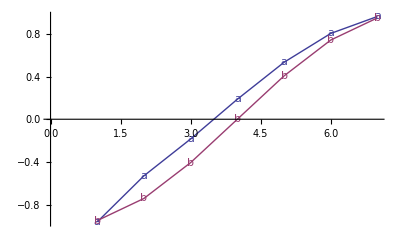

```mathematica
ListLinePlot[{2*parameters[[1]] - 1, pts},PlotMarkers->{"a","b"}]
```